Quantum Operations

Definitionpaclet:QuantumMob/Q3S/tutorial/QuantumOperations#339532637 | Unitary Representationpaclet:QuantumMob/Q3S/tutorial/QuantumOperations#1215528911
Kraus Representationpaclet:QuantumMob/Q3S/tutorial/QuantumOperations#982874389 | Measurements as Quantum Operationspaclet:QuantumMob/Q3S/tutorial/QuantumOperations#1580488278
Choi Isomorphismpaclet:QuantumMob/Q3S/tutorial/QuantumOperations#2111356922 | Examplespaclet:QuantumMob/Q3S/tutorial/QuantumOperations#269244870

See also Section 5.2 and Appendix B of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

Under a certain physical process, the state of a given system evolves into another state. The time evolution of a closed system is described by unitary operators. For an open quantum system, which interacts with its environment, the evolution is not unitary any longer.
Dynamical processes of open quantum systems are described by a special kind of supermaps called quantum operations. A quantum operation transforms density operators to other density operators while preserving the elementary properties of density operators. In particular, density operators are positive, so a quantum operation needs to preserve positivity. However, it turns out that merely preserving positivity is not sufficient and a much stronger condition is required. Imagine that a system has interacted with its surroundings and established an entanglement with them. Physically, one expects the operation to preserve the properties, positivity in particular, of the density operator of the whole containing the system and surroundings. Essentially, a quantum operation needs to preserve not only the positivity of density operators of a given system but also all density operators of any extended system including the system itself and its surrounding systems. Mathematically, such a condition is satisfied by completely positive supermaps.

Supermappaclet:QuantumMob/Q3S/ref/SupermapQuantumMob Package Symbol | Describes the quantum operations
ChoiMatrixpaclet:QuantumMob/Q3S/ref/ChoiMatrixQuantumMob Package Symbol | The Choi matrix of a supermap

Functions useful to handle quantum operations.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
Needs["QuamtumMob`Q3`"]
```

Throughout this documentation, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Definition

A supermap is a linear mapping of linear operators. Recall that linear operators on a vector space 𝒱 themselves form a vector space ℒ(𝒱). A considerable amount of interest in supermaps came with the booming of quantum information theory in the 1990s when it became clear that supermaps are important in the study of entanglement. Since then, mathematical theories on supermaps have been developed at a notably fast pace and applied to a wide range of subjects in quantum computation and quantum information.

A quantum operation is a special kind of supermap. Let 𝒱 and 𝒲 be vector spaces. Suppose that ℱ is a supermap from ℒ(𝒱) onto ℒ(𝒲). ℱ is called a quantum operation if it satisfies the following three axioms.

ℱ never increases the trace. That is, 0≤Tr[ ℱ(ρ)]≤1 for any density operator ρ.

ℱ is convex linear. That is, for any probabilities p_j and density operators ρ_j on 𝒱,

ℱ(∑_j ρ_j p_j)=∑_j ℱ(ρ_j)p_j.

ℱ is a completely positive supermap. That is, not only ℱ(ρ) itself is positive for any positive operator ρ on 𝒱, but (ℱ⊗ℐ)(ρ) is also positive for any positive operator on 𝒱⊗ℰ with an arbitrary vector space ℰ.

Physically, the vector space ℰ in (c) above is associated with an environment. ℱ⊗ℐ acts non-trivially only on 𝒱 associated with the system but trivially on ℰ. To be physically meaningful, ℱ⊗ℐ is expected to preserve the properties, especially positivity, of density operators ρ on 𝒱⊗ℰ. Note that ρ may contain a considerable amount of entanglement due to prior interactions between the system and environment.

Most quantum operations preserve the trace. That is, Tr[ ℱ(ρ)]=1 for all density operators ρ. An important exception is the process associated with a (generalized selective) measurement. When the trace is not preserved, Tr[ ℱ(ρ)]=1 gives the probability for the dynamical process ℱ to occur.

In quantum information theory, quantum operations preserving trace, i.e., completely positive and trace-preserving supermaps, are called quantum channels. Physically, these describe communication channels that can transmit quantum information, as well as classical information.

Another important class of physical phenomena described by quantum operations is quantum decoherence or just decoherence for short, referring to the loss of quantum coherence. We have briefly introduced this effect in the previous section through toy models. Quantum operations offer a complete and general description of decoherence.

Kraus Representation

A quantum operation is a restricted form of completely positive supermap. Accordingly, for any quantum operation ℱ from ℒ(𝒱) onto ℒ(𝒲), there exist linear maps  from 𝒱 onto 𝒲 such that

ℱ(ρ)=Σ_μ F_μ ρ F_μ^†

for all linear operators (not necessarily density operators) ρ on 𝒱. The linear maps F_μ are called the Kraus elements or the Kraus maps of ℱ. Then, the trace-decreasing condition in axiom (a)  imposes the inequalities

0≤Σ_μ F_μ^†F_μ≤1.

One can always choose Kraus elements that are mutually orthogonal with respect to the Hilbert-Schmidt inner product, that is,

Tr[F_μ^†F_ν]=0

whenever μ≠ν. Through the procedure of choosing orthogonal Kraus elements, one can drastically optimize Kraus elements (see below).

The simplest example of the Kraus representation is of the form

ℱ(ρ̂)=Uρ U^†,

involving a single unitary operator. Naturally it describes the unitary dynamics of a closed system. Note that if there are more than one Kraus elements involved in the Kraus representation, the associated dynamics is not unitary even if the Kraus elements are all unitary. For example, consider a supermap

ℱ(ρ)=((1-p)ρ+p/3(XρX+YρY+ZρZ).

Here, all Kraus elements (I,X,Y,Z up to normalization factors) are unitary. However, ℱ causes depolarization in ρ for any non-zero value of p.

The Kraus representation of a quantum operation as a sum of operators provides powerful tools to analyze the quantum operation. However, at this stage, the Kraus representation follows from a mathematical theorem for completely positive supermap. How does the Kraus representation arise physically?

To see how the Kraus representation arises physically, let us consider a system interacting with its environment. We denote with 𝒱 and ℰ the Hilbert spaces associated with the system and environment, respectively. For simplicity, we assume that the total system is initially in the product state ρ⊗σ. The total system is a closed system, and the dynamical process afterwards due to the system-environment interaction is described with an overall unitary operator U acting on the total system, ρ⊗ σ↦U(ρ⊗ σ)U^†. Without access to the environment, one has to take a partial trace of the final state over the environment to obtain the state of the system. Putting it all together, the quantum operation ℱ describing the process is written as

ℱ(ρ)=Tr_ℰ[U(ρ⊗ σ)U^†]=Σ_i ε_iU(ρ⊗ σ)U^†ε_i,

where {ε_i|i=1,2,…,d_ℰ} is an orthonormal basis of ℰ of dimension d_ℰ. On the right-hand side of the above equation, the Hermitian product is applied partially and only on ℰ, and the expression still remains as an operator on 𝒱. To construct the Kraus elements, we first take the spectral decomposition of σ

σ=Σ_(j=1)^r s_js_j,

where r is the rank of σ, and the eigenvectors s_j of σ̂ have been normalized by their own eigenvalues s_j=s_js_j since σ is a positive semidefinite operator. We then define linear maps F_ij:𝒱↦𝒲 for each i and j by

F_ij:=Tr_ℰ[(I⊗ε_is_j)^†U]=ε_iUs_j .

In the quantum circuit model, Figure 1 depicts the above definition. Physically,  F_ij describes the dynamics of the system under the condition that the environment has made a transition from the initial state s_j to state ε_i under the unitary interaction between the system and environment. We finally regard μ:=(i,j) as a collective index and identify F_μ≡F_ij to be the desired Kraus elements. Clearly, they satisfy the closure relation

Σ_μ F_μ^†F_μ=I.

Putting this equation to the expression for ℱ(ρ), we arrive at the representation

ℱ(ρ)=Σ_μ F_ν ρ F_μ^† .

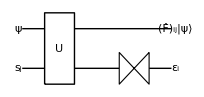

Figure 1. Quantum circuit describing the Kraus element F_ij corresponding to the dynamics of the system on condition that the environment has made a transition from the initial state s_j to state ε_i under the unitary interaction U between the system and environment.

In the above arguments, we have derived a Kraus representation for a quantum operation based on a system-plus-environment model. While it provides a useful physical picture of quantum operations, the resulting representation does not look particularly useful at first glance. The Kraus elements F_μ are not orthogonal to each other with respect to the Hilbert-Schmidt inner product. Even worse, the number of Kraus elements is equal to the dimension of the environmental Hilbert space ℰ and may be huge given that the dimension of ℰ is infinite for any realistic environment. However, neither raises a significant problem. A formal representation in the form of the Kraus representation already facilitates analysis of the quantum operation. Moreover, one can optimize the Kraus elements by reconstructing orthogonal Kraus elements as we see in the next section.

### Optimization of Kraus Representation

Given a set of Kraus elements, how can one actually choose new Kraus elements that are mutually orthogonal. Let {E_μ} be a basis of the space ℒ(𝒱,𝒲) of all linear maps from 𝒱 to 𝒲. We expand F_ν in this basis

F_ν=Σ_μ E_μ M_(μ ν) ,

where M is the matrix of the expansion coefficients. Putting it back to the Kraus representation, we have

ℱ(ρ)=Σ_(μ ν)E_μ ρ (E_ν^†(M M^†))_(μ ν).

The square matrix M M^† of size (dim 𝒱)×(dim 𝒲)  is positive semidefinite, and can be decomposed into M M^†=V Λ V^†, where V is a unitary matrix and Λ is a diagonal matrix with all elements non-negative. We now define new Kraus elements

F'_ν:=(Σ_μ(V √Λ))_(μ ν) .

Then, it is clear that they are mutually orthogonal. Furthermore,

ℱ(ρ)=Σ_μ F'_ν ρ F_μ^(′†) ,

where N≤(dim 𝒱)×(dim 𝒲). Therefore, it is noted that a set of mutually orthogonal Kraus elements is optimal in the sense that it has no more elements than (dim 𝒱)×(dim 𝒲).

### Unitary Freedom of Kraus Elements

(to be completed)

Choi Isomorphism

The Choi isomorphism is a one-to-one correspondence between supermaps and (usual) operators. It allows us to inspect a supermap in terms of the corresponding operator. It can reveal additional properties of the supermap that is not immediately clear from the supermap itself.

One can also use it for physically-motivated proofs of the Kraus representation theorem discussed above in terms of the quantum gate teleportation protocol. For those proofs, we refer interested readers to  Section 5.2.2 of the Quantum Workbook (2022).

Another interesting application of the Choi isomorphism is a rigorous proof of the unitary freedom of Kraus  elements mentioned above. It is not explicitly provided in this document. We refer interested readers to Section 5.2.2 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

Unitary Representation

A quantum operation can always be regarded as a unitary operator on an extended system, which involves an “environment” in addition to the original “system”. Although it is not particularly useful for practical applications, the unitary representation provides a clear physical insight into the underlying physical processes described by the quantum operation.

Suppose that we are given a quantum operation ℱ:ℒ(𝒱)→ℒ(𝒱) specified by the Kraus representation in terms of the Kraus elements F_μ (μ =0,1,. . . ,m−1). As such, we want to construct a system-plus-environment
model that produces the same effect as ℱ when the environment is traced out. Therefore, we need to find a proper vector space ℰ for the environment and an overall unitary operator U acting on the total system 𝒱⊗ℰ such that

ℱ(ρ) =Tr_ℰ [U(ρ⊗ϵ_0ϵ_0)U^†]

for all ρ in ℒ(𝒱) and a particular state ϵ_0 in ℰ. The choice of ϵ_0 is completely arbitrary, and one can even choose a mixed state.

We first construct the vector space ℰ associated with the environment by choosing an orthonormal basis {ϵ_0,ϵ_1,…,ϵ_(m-1)}. Here, just for convenience, we have chosen the basis so as for it to include the state ϵ_0, but it is not necessary. Note that the required dimension m of ℰ is the same as the number of the Kraus elements (F̂)_μ in the Kraus representation and is no larger than (dim𝒱)^2.

Define a unitary operator U on 𝒱⊗ℰ by requiring that

U(ψ⊗ϵ_0)=Σ_μ(Uψ)⊗ϵ_μ

for all ψ in 𝒱. Clearly, taking the partial trace over the environment reproduces ℱ(ψψ) as one can see from an explicit evaluation

Tr_ℰ [U(ψψ⊗ϵ_0ϵ_0)U^†]=Σ_μν Tr_ℰ[(F_μ ψψ F_ν^†)⊗ϵ_μϵ_ν]=Σ_μ F_μ ψψ F_ν^† .

This relation is linear and holds for an arbitrary vector ψ, and hence it should holds for any mixed state 	ρ=∑_j ψ_j p_j ψ_j.

Measurements as Quantum Operations

Generalized measurements can be regarded as a special case of quantum operations. Suppose that a measurement is described by a set of measurement operators M_m corresponding to measurement outcomes m. The mapping ℱ_m from ℒ(𝒱) onto ℒ(𝒱) defined by

ℱ_m(ρ)=M_m ρ M_m^†

for each m is obviously a quantum operation. This is natural since the measurement process involves the interaction of the system with the measuring devices. Note that the quantum operation ℱ_m does not preserve the trace in general,

0≤Tr[ℱ_m(ρ)]≤1 .

Physically, Tr[ℱ_m(ρ)] gives the probability to get outcome m from the measurement process.

The measurement given above is a selective measurement. This physically involves separating an ensemble into subensembles that are distinguished by the measurement outcome. Schwinger (1959) conceived a new notion corresponding to the measurement process prior to the selection stage. It is denominated as a non-selective measurement. One can also regard a non-selective measurement as remixing the subensembles after the measurement with the probabilities p_m:=Tr[ℱ_m(ρ̂)]. A non-selective measurement is thus represented by the quantum operation

ℱ(ρ):=Σ_m ℱ_m(ρ)=Σ_m M_m ρ M_m^† .

In this case, the trace is preserved: Tr [ℱ_m(ρ)]=1 for any density operator ρ̂. This follows from the completeness relation, ∑_m M_m^†M_m=I, satisfied by the measurement operators.

Examples

So far, we discussed a general description of quantum noisy processes in terms of the corresponding quantum operations. Let us now present some examples for a single qubit. We consider some limiting cases that allow us to easily grasp the physical meaning of the Kraus elements.

### Phase Damping

The phase damping process is a decoherence process without involving any relaxation of energy or change in the population over the states. In this sense, it may be regarded as a pure decoherence process without involving any energy relaxation. For this reason, it is also referred to as a dephasing process.

The unitary representation of a phase damping process in a single-qubit system is given by

0⊗ϵ_0↦0⊗ϵ_0 ,

1⊗ϵ_0↦1⊗ϵ_0 √(1-p)+1⊗ϵ_1 √p ,

where {ϵ_0, ϵ_1} is an orthonormal basis of the vector space ℰ associated with the environment. It indicates that when and only when the system is in 1, the environment changes its state from the initial state ϵ_0 to another orthogonal state |ε1⟩ with probability p. Note that the system remains in the same state in both cases. The key point is that the environment nevertheless “knows” which state the system is in and this knowledge leads to a loss of coherence in the state of the system.

Indeed, the total unitary operator is a controlled-U operator with

U≐(√(1-p) | -√p
√p | √(1-p))

in the basis {ϵ_0, ϵ_1}. As a result, when the system is prepared in a coherent superposition, the controlled-U operator creates an entanglement between the system and the environment

(0 c_0+1 c_1)⊗ϵ_0↦0⊗ϵ_0 c_0+1⊗(Uϵ_1)

or, more explicitly,

(0 c_0+1 c_1)⊗ϵ_0↦(0 c_0+1 c_1 √(1-p))⊗ϵ_0+1⊗ϵ_1 c_1 √p .

Due to the entanglement, the final state of the system alone cannot be a pure state and coherence in the initial state has been lost through the process. With the prescription above, the Kraus elements are given by

E_0≐(1 | 0
0 | √(1-p)) ,    E_1≐(0 | 0
0 | √p)

and the corresponding quantum operation is given by

ℱ(ρ)=E_0 ρ E_0^†+E_1 ρ E_1^† .

Note  that  they  are  not  orthogonal,

Tr[E_0^†E_1]=√(p(1-p))≠0.

It is therefore more convenient and efficient to choose mutually orthogonal Kraus elements

F_0=(√(1+√(1-p)))/2 I ,     F_1=(√(1-√(1-p)))/2 Z

In short, the quantum operation for the phase damping process is written as

ℱ(ρ)=(1+√(1-p))/2 ρ+(1-√(1-p))/2 ZρZ

It is also convenient to expand the density operator into

ρ=1/2 I+xX+yY+zZ ,

where x, y, and z are real parameters. Then, the quantum operation ℱ gives

ρ=1/2 I+x √(1-p)X+y √(1-p)Y+zZ ,

Note that the coefficient in Z does not change. It asserts that the populations in 0 and 1, 1/2+z and 1/2-z , do not change. The phase damping process only causes pure dephasing. In particular, at p→1, the new density operator approaches,

ρ→1/2 I+zZ ,

The coherence has disappeared completely.

The phase damping process is specified by two Kraus elements.

```mathematica
Let[Real,p]
ops={Sqrt[(1+Sqrt[1-p])/2],Sqrt[(1-Sqrt[1-p])/2]*S[3]};
spr=Supermap[ops]
```

Supermap[…]

Here, p is the probability for the phase to be flipped.

```mathematica
Let[Real,ρ]
rho=1/2+ρ[{1,2,3}].S[All]
```

1/2+S^X ρ_(,,1)+S^Y ρ_(,,2)+S^Z ρ_(,,3)

The supermap transforms the above density operator as follows.

```mathematica
new=spr[rho]
```

1/2+√(1-p) S^X ρ_(,,1)+√(1-p) S^Y ρ_(,,2)+S^Z ρ_(,,3)

### Amplitude Damping

The amplitude damping process describes the spontaneous decay of the “excited state” 1 of the system to the “ground state” 0. The decay is accompanied by the emission of a photon. One can regards that the photon “observes” the system and the information of the system acquired by the photon leads to decoherence.

In the unitary representation, the process is described by the overall unitary operator such that

0⊗ϵ_0↦0⊗ϵ_0 ,

1⊗ϵ_0↦1⊗ϵ_0 √(1-p)+0⊗ϵ_1 √p ,

Thus, the decay occurs with probability p provided that the system is in the state 1. The Kraus elements are given by

F_0≐(1 | 0
0 | √(1-p)) ,    F_1≐(0 | √p
0 | 0) .

They are already orthogonal to each other. The quantum operation describing the amplitude damping process reads as

ℱ(ρ)=F_0 ρ F_0^†+F_1 ρ F_1^† .

With the expansion of the density operator ρ,

ρ=1/2 I+xX+yY+zZ ,

the above operation reads as

ρ=1/2 I+(1-p)xX+(1-p)yY+(1/2+(1-p)z)Z .

In the limit of p→1, the new density operator approaches the pure state 0,

ρ→1/2 I+1/2 Z=00 .

regardless of the initial state. This is due to the relaxation from 1 to 0.

The amplitude damping process is specified by two Kraus elements.

```mathematica
Let[Real,p]
ops={S[10]+Sqrt[1-p]*S[11],Sqrt[p]*S[4]};
spr=Supermap[ops]
```

Supermap[…]

Here, p is the probability for the phase to be flipped.

```mathematica
Let[Real,ρ]
rho=1/2+ρ[{1,2,3}].S[All]
```

1/2+S^X ρ_(,,1)+S^Y ρ_(,,2)+S^Z ρ_(,,3)

The supermap transforms the above density operator as follows.

```mathematica
new=spr[rho]//Elaborate
```

1/2+√(1-p) S^X ρ_(,,1)+√(1-p) S^Y ρ_(,,2)+S^Z (p (1/2-ρ_(,,3))+ρ_(,,3))

### Depolarizing

In the depolarizing process, the decoherence occurs symmetrically, and there is no distinction of the specific types of actual decoherence processes. The system undergoes an incoherent process with probability p and remains intact with probability 1−p. The incoherent process may cause the system to flip the bit value, the phase, or both with equal probability.

The situation can be best described in the unitary representation. Suppose that the system and the environment is in the product state ψ⊗ϵ_0. The decoherence process causes the transition

ψ⊗ϵ_0↦ψ⊗ϵ_0 √(1-p)+((Xψ)⊗ϵ_1+(Yψ)⊗ϵ_2+(Zψ)⊗ϵ_3)√(p/3) .

The environment evolves to one of the four mutually orthogonal states ϵ_0, ϵ_1, ϵ_2, ϵ_3. The final states of the environment enables recognizing the process that has occurred (bit flip, phase flip, or both). This causes decoherence on the state of the system.

From the above unitary representation, we can get the Kraus elements

F_0=√(1-p)I ,     F_1=√(p/3)X,     F_2=√(p/3)Y,     F_3=√(p/3)Z,

The Kraus elements are already orthogonal to each other. One can also check that they satisfy the completeness relation

F_0^†F_0+F_1^†F_1+F_2^†F_2+F_3^†F_3=I

as they should. In the Kraus representation with the above Kraus elements, a density operator ρˆ is transformed under the decoherence process as

ℱ(ρ)=(1-p)ρ+p/3(XρX+YρY+ZρZ) .

In terms of the components in the expansion

ρ=1/2 I+xX+yY+zZ ,

it reads as
	ℱ(ρ) = 1/2 I +(1-(4p)/3)(xX+yY+zZ) .

This implies that under the process, the “spin” polarization (i.e., the Bloch vector corresponding to the resulting density operator)

P:=(⟨X⟩,⟨Y⟩,⟨Z⟩)

shrinks by the factor (1−4p/3). Hence the name of the process. The state becomes completely random for 4p/3=1.

The depolarizing process is specified by three Kraus elements.

```mathematica
Let[Real,p]
ops=Prepend[Sqrt[p/3]*S[All],Sqrt[1-p]];
spr=Supermap[ops]
```

Supermap[…]

Here, p is the probability for the phase to be flipped.

```mathematica
Let[Real,ρ]
rho=1/2+ρ[{1,2,3}].S[All]
```

1/2+S^X ρ_(,,1)+S^Y ρ_(,,2)+S^Z ρ_(,,3)

The supermap transforms the above density operator as follows.

```mathematica
new=spr[rho]
```

1/2+(1-(4 p)/3) S^X ρ_(,,1)+(1-(4 p)/3) S^Y ρ_(,,2)+(1-(4 p)/3) S^Z ρ_(,,3)

| Related Guides
▪Quantum Information Systems
▪Q3

| Related Tech Notes
▪Choi Isomorphism
▪Quantum Noise and Decoherence
▪Quantum Information Systems with Q3
▪Q3: Quick Start

| Related Links
▪J. Schwinger, Proceedings of the National Academy of Sciences 45, 1542 (1959)https://doi.org/10.1073/pnas.45.10.1542, "The Algebra of Microscopic Measurement".
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).